```mathematica
(*Tunneling Density of States*)
{Qx,Des,Ded}={1.322,0.6173618651864763,1.5842712447013014};
mu=-.31
ClearAll[f]
f[k_,eps0_,eps1_,eps2_,Δ1_,Δ2_]:=With[{ω=Exp[(2 π I)/3],t1=2^(1/3),t2=2^(2/3)},Module[{A,B,disc,c},A=9 Δ1^2 eps0+9 Δ2^2 eps0+2 eps0^3-9 Δ1^2 eps1+18 Δ2^2 eps1+3 eps0^2 eps1-3 eps0 eps1^2-2 eps1^3+18 Δ1^2 eps2-9 Δ2^2 eps2+3 eps0^2 eps2+12 eps0 eps1 eps2+3 eps1^2 eps2-3 eps0 eps2^2+3 eps1 eps2^2-2 eps2^3;
B=-(eps0-eps1-eps2)^2-3 (Δ1^2+Δ2^2+eps0 eps1+eps0 eps2-eps1 eps2);
disc=Sqrt[A^2+4 B^3];
c=(A+disc)^(1/3);
(eps0-eps1-eps2)/3+(ω^k*c-ω^(-k)*t2*B/c)/(3*t1)]]

Factor1[E1_,E2_,E3_,eps1_,eps2_]:=(E1+eps1) (E1+eps2)/((E1-E2) (E1-E3))

Factor2[E1_,E2_,E3_,eps1_,Δ_]:=Δ*(E1+eps1)/((E1-E2) (E1-E3))

t=1;tprime=0.3 t;
Qy=0;
Dispersion[x_,y_]:=-2 t (Cos[x]+Cos[y])+4 tprime Cos[x] Cos[y]-mu;

Jx[x_,y_]:=2 t Sin[x]-4 Cos[y] Sin[x] tprime;
Jy[x_,y_]:=2 t Sin[y]-4 Cos[x] Sin[y] tprime;

Shaped[x_,y_]:=Cos[x]-Cos[y];
Shapes[x_,y_]:=Cos[x]+Cos[y];
Netshape[x_,y_]:=Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y];
fepsi[x_,y_]:=Dispersion[x,y];
fepsi1[x_,y_]:=Dispersion[x-Qx,y-Qy];
fepsi2[x_,y_]:=Dispersion[x+Qx,y+Qy];

Band1[x_,y_]:=f[1,fepsi[x,y],fepsi1[x,y],fepsi2[x,y],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];
Band2[x_,y_]:=f[2,fepsi[x,y],fepsi1[x,y],fepsi2[x,y],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];
Band3[x_,y_]:=f[3,fepsi[x,y],fepsi1[x,y],fepsi2[x,y],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];

Thermal[E_,T_]:=1/(Exp[E/T]+1);

DiracN[x_,sigma_]:=1/(Sqrt[2 Pi sigma]) Exp[-(x^2)/(2 sigma)];
ThermalD[x_,T_]:=-(ⅇ^(x/T)/((1+ⅇ^(x/T))^2 T)); 

IntGG[T_,px_,py_]:=Module[{cx,cy0,cy,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
kx=1/10^7;ky=0; fre=0;
pxp=px+kx/2;pxn=px-kx/2;
pyp=py+ky/2;pyn=py-ky/2;
E1p=Band1[pxp,pyp];E2p=Band2[pxp,pyp];E3p=Band3[pxp,pyp];
Ep={E1p,E2p,E3p};
E1n=Band1[pxn,pyn];E2n=Band2[pxn,pyn];E3n=Band3[pxn,pyn];
En={E1n,E2n,E3n};
(**)
eps1p=fepsi1[pxp,pyp];eps2p=fepsi2[pxp,pyp];
eps1n=fepsi1[pxn,pyn];eps2n=fepsi2[pxn,pyn];
(**)
g1n=Factor1[E1n,E2n,E3n,eps1n,eps2n];g2n=Factor1[E2n,E1n,E3n,eps1n,eps2n];g3n=Factor1[E3n,E1n,E2n,eps1n,eps2n];
g1p=Factor1[E1p,E2p,E3p,eps1p,eps2p];g2p=Factor1[E2p,E1p,E3p,eps1p,eps2p];g3p=Factor1[E3p,E1p,E2p,eps1p,eps2p];
dis1n=Thermal[E1n,T];dis2n=Thermal[E2n,T];dis3n=Thermal[E3n,T];
dis1p=Thermal[E1p,T];dis2p=Thermal[E2p,T];dis3p=Thermal[E3p,T];
(**)
gn={g1n,g2n,g3n};gp={g1p,g2p,g3p};
disn={dis1n,dis2n,dis3n};disp={dis1p,dis2p,dis3p};
(**)
result0=Sum[If[i!=j,(disp[[j]]-disn[[i]])/(Ep[[j]]-En[[i]])*gn[[i]]*gp[[j]],0],{i,1,3},{j,1,3}];
result1=Sum[ThermalD[En[[i]],T]*gn[[i]]*gp[[i]],{i,1,3}];
result=result0+result1;
(*now let us add the current operator*)
cx=Jx[px,py];cy=Jy[px,py];
(*For definiteness let us consider y-direction response*)
Result=result*cx*cx
]

IntGGIntegrated[T_]:=NIntegrate[IntGG[T,px,py],{px,-Pi,Pi},{py,-Pi,Pi}, Method->{"LocalAdaptive"}];


IntFF[T_,px_,py_]:=Module[{cx0,cx,Pshape,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
kx=1/10^7;ky=0; fre=0;
pxp=px+kx/2;pxn=px-kx/2;
pyp=py+ky/2;pyn=py-ky/2;
E1p=Band1[pxp,pyp];E2p=Band2[pxp,pyp];E3p=Band3[pxp,pyp];
Ep={E1p,E2p,E3p};
E1n=Band1[pxn,pyn];E2n=Band2[pxn,pyn];E3n=Band3[pxn,pyn];
En={E1n,E2n,E3n};
eps1p=fepsi1[pxp,pyp];eps2p=fepsi2[pxp,pyp];
eps1n=fepsi1[pxn,pyn];eps2n=fepsi2[pxn,pyn];
(**)
Pshape=Des*Shapes[pxp+Qx/2,pyp]+Ded*Shaped[pxp+Qx/2,pyp];
Nshape=Des*Shapes[pxn+Qx/2,pyn]+Ded*Shaped[pxn+Qx/2,pyn];
(**)
g1n=Factor2[E1n,E2n,E3n,eps1n,Nshape];g2n=Factor2[E2n,E1n,E3n,eps1n,Nshape];g3n=Factor2[E3n,E1n,E2n,eps1n,Nshape];
g1p=Factor2[E1p,E2p,E3p,eps1p,Pshape];g2p=Factor2[E2p,E1p,E3p,eps1p,Pshape];g3p=Factor2[E3p,E1p,E2p,eps1p,Pshape];
(**)
dis1n=Thermal[E1n,T];dis2n=Thermal[E2n,T];dis3n=Thermal[E3n,T];
dis1p=Thermal[E1p,T];dis2p=Thermal[E2p,T];dis3p=Thermal[E3p,T];
(**)
gn={g1n,g2n,g3n};gp={g1p,g2p,g3p};
disn={dis1n,dis2n,dis3n};disp={dis1p,dis2p,dis3p};
(**)
result0=Sum[If[i!=j,(disp[[j]]-disn[[i]])/(Ep[[j]]-En[[i]])*gn[[i]]*gp[[j]],0],{i,1,3},{j,1,3}];
result1=Sum[ThermalD[En[[i]],T]*gn[[i]]*gp[[i]],{i,1,3}];
result=result0+result1;
(**)
(*now let us add the current operator*)
cx0=Jx[px,py];cx=Jx[px+Qx,py+Qy];
(*For definiteness let us consider y-direction response*)
Result=result*cx*cx0
]

IntFFN[T_,px_,py_]:=Module[{cx0,cx,Pshape,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
kx=1/10^7;ky=0; fre=0;
pxp=px+kx/2;pxn=px-kx/2;
pyp=py+ky/2;pyn=py-ky/2;
E1p=Band1[pxp,pyp];E2p=Band2[pxp,pyp];E3p=Band3[pxp,pyp];
Ep={E1p,E2p,E3p};
E1n=Band1[pxn,pyn];E2n=Band2[pxn,pyn];E3n=Band3[pxn,pyn];
En={E1n,E2n,E3n};
eps1p=fepsi1[pxp,pyp];eps2p=fepsi2[pxp,pyp];
eps1n=fepsi1[pxn,pyn];eps2n=fepsi2[pxn,pyn];
(**)
Pshape=Des*Shapes[pxp-Qx/2,pyp]+Ded*Shaped[pxp-Qx/2,pyp];
Nshape=Des*Shapes[pxn-Qx/2,pyn]+Ded*Shaped[pxn-Qx/2,pyn];
(**)
g1n=Factor2[E1n,E2n,E3n,eps2n,Nshape];g2n=Factor2[E2n,E1n,E3n,eps2n,Nshape];g3n=Factor2[E3n,E1n,E2n,eps2n,Nshape];
g1p=Factor2[E1p,E2p,E3p,eps2p,Pshape];g2p=Factor2[E2p,E1p,E3p,eps2p,Pshape];g3p=Factor2[E3p,E1p,E2p,eps2p,Pshape];
(**)
dis1n=Thermal[E1n,T];dis2n=Thermal[E2n,T];dis3n=Thermal[E3n,T];
dis1p=Thermal[E1p,T];dis2p=Thermal[E2p,T];dis3p=Thermal[E3p,T];
(**)
gn={g1n,g2n,g3n};gp={g1p,g2p,g3p};
disn={dis1n,dis2n,dis3n};disp={dis1p,dis2p,dis3p};
(**)
result0=Sum[If[i!=j,(disp[[j]]-disn[[i]])/(Ep[[j]]-En[[i]])*gn[[i]]*gp[[j]],0],{i,1,3},{j,1,3}];
result1=Sum[ThermalD[En[[i]],T]*gn[[i]]*gp[[i]],{i,1,3}];
result=result0+result1;
(**)
(*now let us add the current operator*)
cx0=Jx[px,py];cx=Jx[px-Qx,py-Qy];
(*For definiteness let us consider y-direction response*)
Result=result*cx*cx0
]

IntFFIntegrated[T_]:=NIntegrate[IntFF[T,px,py],{px,-Pi,Pi},{py,-Pi,Pi}, Method->{"LocalAdaptive"}];
IntFFNIntegrated[T_]:=NIntegrate[IntFFN[T,px,py],{px,-Pi,Pi},{py,-Pi,Pi}, Method->{"LocalAdaptive"}];

xx=Table[ IntGGIntegrated[x],{x,0.008,0.1,0.02}]
xx1=Table[ IntFFIntegrated[x],{x,0.008,0.1,0.02}]
```

-0.31

{-8.25191+4.84859×10^-16 ⅈ,-8.25455+1.0268×10^-16 ⅈ,-8.26081+3.95031×10^-16 ⅈ,-8.27106+1.76489×10^-16 ⅈ,-8.2831+2.6425×10^-16 ⅈ}

{-1.09028-1.17349×10^-15 ⅈ,-1.09488-8.4798×10^-16 ⅈ,-1.1065-1.25324×10^-15 ⅈ,-1.12562-1.42938×10^-15 ⅈ,-1.14666-1.31636×10^-15 ⅈ}

```mathematica
diagmxx={11.436815161000398,11.4371047177733,11.437802727189936,11.439038998082365,11.440714400442328};
```

4 π^2

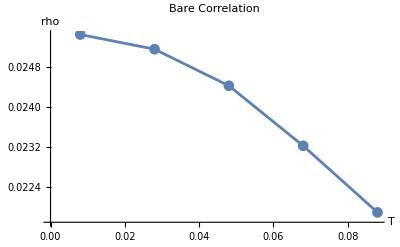

```mathematica
xValues=Range[0.008,0.1,0.02];
factor=(2*Pi)^2
data=Transpose[{xValues,Re[xx+xx1*2+diagmxx]/factor}];
data1=Transpose[{xValues,Re[xx1*4]}];
ListPlot[{data },Joined->True,PlotMarkers->Automatic,AxesLabel->{"T","rho"},PlotLabel->"Bare Correlation"]
```

```mathematica
Col=-{0.04836225837842864,0.048641759483460674,0.049323551199150495,0.05045391678043148,0.051829971947855435};
```

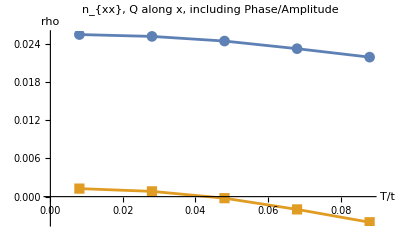

```mathematica
xValues=Range[0.008,0.1,0.02];
RRR=Re[(xx+xx1*2+diagmxx)/factor+Col/2];
dataRRR=Transpose[{xValues,RRR}];

ListPlot[{data,dataRRR},Joined->True,PlotMarkers->Automatic,AxesLabel->{"T/t","rho"},PlotLabel->"n_{xx}, Q along x, including Phase/Amplitude"]
```